## Bose-Hubbard model simulation

References:
	F. Verstraete, V. Murg, J. I. Cirac
	Matrix product states, projected entangled pair states, and variational renormalization group methods for quantum spin systems
	Advances in Physics 57, 143-224 (2008) DOI

	Thomas Barthel
	Precise evaluation of thermal response functions by optimized density matrix renormalization group schemes
	New Journal of Physics 15, 073010 (2013) DOI

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
SparseIdentityMatrix[d_]:=SparseArray[{i_,i_}->1,{d,d}]
```

```mathematica
SiteCreateOp[M_]:=DiagonalMatrix[Sqrt[Range[1,M]],-1]
SiteAnnihilOp[M_]:=DiagonalMatrix[Sqrt[Range[1,M]],1]
```

```mathematica
NumberOp[M_]:=DiagonalMatrix[Range[0,M]]
```

```mathematica
Z[H_,β_]:=Norm[MatrixExp[-β/2 H],"Frobenius"]^2
```

```mathematica
(* construct Bose-Hamiltonian with open boundary conditions *)
Subscript[H, bose][t_,U_,μ_,M_,1]:=U/2 NumberOp[M].(NumberOp[M]-IdentityMatrix[M+1])-μ NumberOp[M]
Subscript[H, bose][t_,U_,μ_,M_,L_]:=-t Sum[KroneckerProduct[SparseIdentityMatrix[(M+1)^(l-1)],SiteCreateOp[M],SiteAnnihilOp[M],SparseIdentityMatrix[(M+1)^(L-l-1)]]+KroneckerProduct[SparseIdentityMatrix[(M+1)^(l-1)],SiteAnnihilOp[M],SiteCreateOp[M],SparseIdentityMatrix[(M+1)^(L-l-1)]],{l,1,L-1}]+Sum[KroneckerProduct[SparseIdentityMatrix[(M+1)^(l-1)],U/2 NumberOp[M].(NumberOp[M]-IdentityMatrix[M+1])-μ NumberOp[M],SparseIdentityMatrix[(M+1)^(L-l)]],{l,1,L}]
```

```mathematica
χC[A_,B_,H_,β_,t_]:=Module[{tA=t/2,tB=t/2,ρβ=MatrixExp[-β/2 H]},1/Z[H,β] Tr[(MatrixExp[ⅈ tB H].ρβ.B.MatrixExp[-ⅈ tB H]).(MatrixExp[-ⅈ tA H].A.ρβ.MatrixExp[ⅈ tA H])]]
```

```mathematica
Subscript[A, op][n_,M_,L_]:=KroneckerProduct[SparseIdentityMatrix[(M+1)^(n-1)],NumberOp[M],SparseIdentityMatrix[(M+1)^(L-n)]]
```

```mathematica
(* local Hamiltonian terms acting on neighboring lattice sites *)
h2[t_,U_,μ_,M_,L_]:=Module[{bd=SiteCreateOp[M],b=SiteAnnihilOp[M],S=U/2 NumberOp[M].(NumberOp[M]-IdentityMatrix[M+1])-μ NumberOp[M],SI,IS},SI=KroneckerProduct[S,IdentityMatrix[M+1]];IS=KroneckerProduct[IdentityMatrix[M+1],S];Table[-t(KroneckerProduct[bd,b]+KroneckerProduct[b,bd])+If[j==1,SI+1/2 IS,If[j<L-1,1/2(SI+IS),1/2 SI+IS]],{j,L-1}]]
```

```mathematica
(* kinetic hopping parameter *)
Subscript[tH, val]=1;
```

```mathematica
(* interaction strength *)
Subscript[U, val]=5;
```

```mathematica
(* chemical potential *)
Subscript[μ, val]=1/7;
```

```mathematica
(* number of lattice sites *)
Subscript[L, val]=6;
```

```mathematica
(* single site occupation number cut-off *)
Subscript[M, val]=2;
```

```mathematica
(* inverse temperature *)
Subscript[β, val]=3/5;
```

```mathematica
(* check *)
Block[{t,U,μ,M=Subscript[M, val],L=Subscript[L, val]},Norm[Flatten[FullSimplify[Sum[KroneckerProduct[SparseIdentityMatrix[(M+1)^(l-1)],h2[t,U,μ,M,L]⟦l⟧,SparseIdentityMatrix[(M+1)^(L-l-1)]],{l,1,L-1}]-Subscript[H, bose][t,U,μ,M,L]]]]]
```

0

```mathematica
(* MPO representing identity operation *)
Subscript[A, id]=Table[ArrayReshape[IdentityMatrix[Subscript[M, val]+1],{Subscript[M, val]+1,Subscript[M, val]+1,1,1}],{i,Subscript[L, val]}]
Dimensions[%]
```

{{{{{1}},{{0}},{{0}}},{{{0}},{{1}},{{0}}},{{{0}},{{0}},{{1}}}},{{{{1}},{{0}},{{0}}},{{{0}},{{1}},{{0}}},{{{0}},{{0}},{{1}}}},{{{{1}},{{0}},{{0}}},{{{0}},{{1}},{{0}}},{{{0}},{{0}},{{1}}}},{{{{1}},{{0}},{{0}}},{{{0}},{{1}},{{0}}},{{{0}},{{0}},{{1}}}},{{{{1}},{{0}},{{0}}},{{{0}},{{1}},{{0}}},{{{0}},{{0}},{{1}}}},{{{{1}},{{0}},{{0}}},{{{0}},{{1}},{{0}}},{{{0}},{{0}},{{1}}}}}

{6,3,3,1,1}

```mathematica
Subscript[t, list]=Range[0,5,1/4];
Length[%]
```

21

```mathematica
(* read simulation results from disk *)
Subscript[χ, list]=First[#]+ⅈ Last[#]&/@Partition[Import["../output/bose_hubbard/L"<>ToString[Subscript[L, val]]<>"/bose_hubbard_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]]<>"_chi.dat","Real64"],2]
Dimensions[%]
```

{0.455586+0. ⅈ,0.452828+0.00568635 ⅈ,0.466222+0.0214818 ⅈ,0.491811+0.0181922 ⅈ,0.498517+0.00859103 ⅈ,0.506315+0.0136878 ⅈ,0.523634+0.00571308 ⅈ,0.518559-0.0155401 ⅈ,0.495102-0.0230783 ⅈ,0.472738-0.0173559 ⅈ,0.45981+0.00224756 ⅈ,0.475541+0.0304601 ⅈ,0.517537+0.0397428 ⅈ,0.552074+0.0210226 ⅈ,0.55734-0.00636098 ⅈ,0.538436-0.0242103 ⅈ,0.51047-0.0273559 ⅈ,0.486463-0.0181837 ⅈ,0.476036+0.00060507 ⅈ,0.488668+0.0200562 ⅈ,0.515961+0.0218782 ⅈ}

{21}

```mathematica
Subscript[j, A]=2;
Subscript[j, B]=4;
```

```mathematica
(* reference calculation *)
Block[{tH=Subscript[tH, val],U=Subscript[U, val],μ=Subscript[μ, val],M=Subscript[M, val],L=Subscript[L, val],β=Subscript[β, val],HB},HB=N[Subscript[H, bose][tH,U,μ,M,L]];Subscript[χ, list,ref]=Table[χC[N[Subscript[A, op][Subscript[j, A],M,L]],N[Subscript[A, op][Subscript[j, B],M,L]],HB,β,t],{t,Subscript[t, list]}]]
```

{0.455543,0.452777+0.0056824 ⅈ,0.466165+0.0214869 ⅈ,0.491765+0.0182011 ⅈ,0.498476+0.00859003 ⅈ,0.506264+0.013682 ⅈ,0.523578+0.00571281 ⅈ,0.518508-0.0155364 ⅈ,0.495053-0.0230793 ⅈ,0.472681-0.0173569 ⅈ,0.459757+0.00225351 ⅈ,0.475498+0.0304609 ⅈ,0.517489+0.0397383 ⅈ,0.552023+0.0210229 ⅈ,0.557294-0.00635669 ⅈ,0.538395-0.0242068 ⅈ,0.510427-0.0273592 ⅈ,0.486409-0.0181865 ⅈ,0.475981+0.000609824 ⅈ,0.488619+0.0200603 ⅈ,0.515913+0.0218807 ⅈ}

```mathematica
(* compare *)
Abs[Subscript[χ, list]-Subscript[χ, list,ref]]
```

{0.0000429034,0.000051356,0.0000576912,0.0000470166,0.0000411886,0.0000508647,0.0000559262,0.0000507667,0.0000489721,0.0000571915,0.0000536836,0.0000433996,0.0000476034,0.0000506717,0.000046298,0.0000404954,0.0000430695,0.0000547426,0.0000553611,0.0000495887,0.0000484113}

```mathematica
Subscript[plot, label]="Bose-Hubbard model with\nt_H="<>ToString[Subscript[tH, val]]<>", U="<>ToString[Subscript[U, val]]<>", μ="<>ToString[InputForm[Subscript[μ, val]]]<>", M="<>ToString[Subscript[M, val]]<>", L="<>ToString[Subscript[L, val]]<>", β="<>ToString[N[Subscript[β, val]]]<>" (scheme C)\nA: number operator at site "<>ToString[Subscript[j, A]]<>", B: number operator at site "<>ToString[Subscript[j, B]];
```

```mathematica
Subscript[fn, export]="plots/"<>#<>"/"<>#<>"_"&[FileBaseName[NotebookFileName[]]];
```

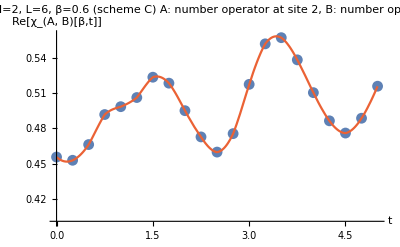

```mathematica
Show[ListPlot[Transpose[{Subscript[t, list],Re[Subscript[χ, list]]}],PlotRange->{Automatic,{0.4,0.56}},AxesLabel->{"t","Re[χ_(A, B)[β,t]]"},PlotLabel->Subscript[plot, label]<>"\nred: independent reference calculation"],Plot[Interpolation[Transpose[{Subscript[t, list],Re[Subscript[χ, list,ref]]}]][τ],{τ,0,5},PlotRange->All,PlotStyle->ColorData[97][4]]]
Export[Subscript[fn, export]<>"chiAB_L"<>ToString[Subscript[L, val]]<>".pdf",%];
```

```mathematica
Subscript[t, plot]=Range[0,5];
```

{{1,9,22,22,22,9,1},{1,9,31,30,22,9,1},{1,9,41,39,26,9,1},{1,9,53,48,33,9,1},{1,9,71,70,42,9,1},{1,9,79,95,53,9,1},{1,9,81,129,71,9,1},{1,9,81,184,79,9,1},{1,9,81,257,81,9,1},{1,9,81,340,81,9,1},{1,9,81,423,81,9,1},{1,9,81,495,81,9,1},{1,9,81,554,81,9,1},{1,9,81,598,81,9,1},{1,9,81,627,81,9,1},{1,9,81,650,81,9,1},{1,9,81,667,81,9,1},{1,9,81,680,81,9,1},{1,9,81,688,81,9,1},{1,9,81,694,81,9,1},{1,9,81,698,81,9,1}}

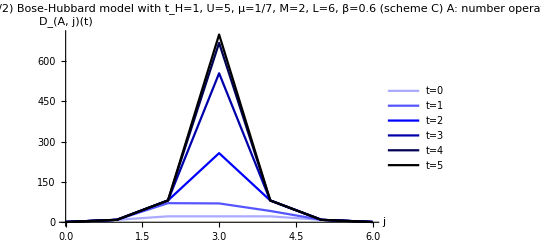

```mathematica
(* virtual bond dimension for 'A' operator *)
Partition[Import["../output/bose_hubbard/L"<>ToString[Subscript[L, val]]<>"/bose_hubbard_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]]<>"_DXA.dat","Integer64"],Subscript[L, val]+1]
%⟦#⟧&/@Flatten[Position[Subscript[t, list],#]&/@Subscript[t, plot]];
ListLinePlot[Transpose[{Range[0,Subscript[L, val]],#}]&/@%,AxesLabel->{"j","D_(A, j)(t)"},PlotRange->All,PlotLabel->"virtual bond dimension of ⅇ^(-ⅈ H t/2) A ⅇ^(-β H/2) ⅇ^(ⅈ H t/2)\n"<>Subscript[plot, label],PlotStyle->{Lighter[Blue,2/3],Lighter[Blue,1/3],Blue,Darker[Blue,1/3],Darker[Blue,2/3],Black},PlotLegends->("t="<>ToString[InputForm[#]]&/@Subscript[t, plot])]
Export[Subscript[fn, export]<>"DA_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]]<>".pdf",%];
```

{{1,9,22,22,22,9,1},{1,9,28,32,32,9,1},{1,9,37,43,41,9,1},{1,9,45,58,53,9,1},{1,9,62,83,72,9,1},{1,9,77,114,81,9,1},{1,9,81,159,81,9,1},{1,9,81,226,81,9,1},{1,9,81,311,81,9,1},{1,9,81,404,81,9,1},{1,9,81,492,81,9,1},{1,9,81,558,81,9,1},{1,9,81,606,81,9,1},{1,9,81,638,81,9,1},{1,9,81,660,81,9,1},{1,9,81,675,81,9,1},{1,9,81,686,81,9,1},{1,9,81,694,81,9,1},{1,9,81,699,81,9,1},{1,9,81,704,81,9,1},{1,9,81,707,81,9,1}}

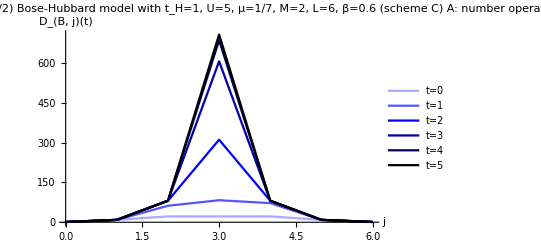

```mathematica
(* virtual bond dimension for 'B' operator *)
Partition[Import["../output/bose_hubbard/L"<>ToString[Subscript[L, val]]<>"/bose_hubbard_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]]<>"_DXB.dat","Integer64"],Subscript[L, val]+1]
%⟦#⟧&/@Flatten[Position[Subscript[t, list],#]&/@Subscript[t, plot]];
ListLinePlot[Transpose[{Range[0,Subscript[L, val]],#}]&/@%,AxesLabel->{"j","D_(B, j)(t)"},PlotRange->All,PlotLabel->"virtual bond dimension of ⅇ^(ⅈ H t/2) ⅇ^(-β H/2) B ⅇ^(-ⅈ H t/2)\n"<>Subscript[plot, label],PlotStyle->{Lighter[Blue,2/3],Lighter[Blue,1/3],Blue,Darker[Blue,1/3],Darker[Blue,2/3],Black},PlotLegends->("t="<>ToString[InputForm[#]]&/@Subscript[t, plot])]
Export[Subscript[fn, export]<>"DB_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]]<>".pdf",%];
```